```mathematica
(* import video *)
filename="/Users/asudler/Desktop/OU/coursework/2023/fall/PHYS-3302-ALAB1/cavendish/mathematica-and-videos/runs/run2.MOV";
frames=Import[filename,"ImageList"];
```

```mathematica
(* find good cropping dimensions *)
Manipulate[ImageTake[frames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
(* crop frames *)
length=Length[frames];
ymin=230;
ymax=370;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
croppedFrames[[1]]
```

-Graphics-

```mathematica
length
```

681

```mathematica
(* binarize data *)
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
(* get center pixel coordinates *)
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

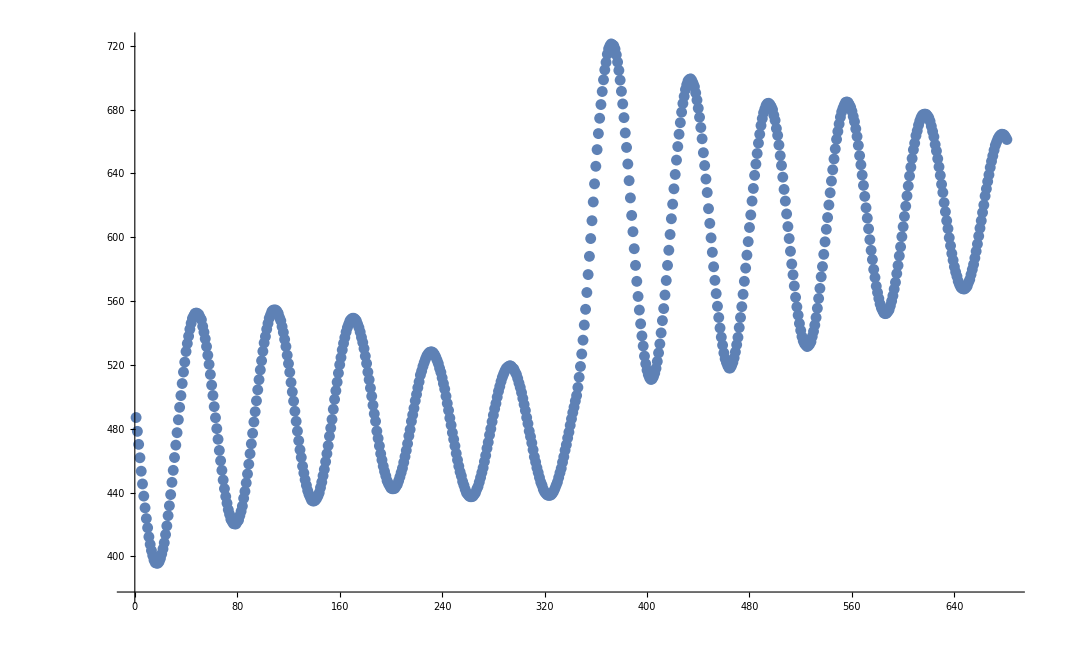

```mathematica
ListPlot[Transpose[xvals]]
```

```mathematica
frames[[1]]
```

-Graphics-

```mathematica
frames[[-1]]
```

-Graphics-

```mathematica
(95.4-.63333)/length
```

0.139158

```mathematica
%*60
```

8.34949